```mathematica
beta=Table[i/20.0,{i,1,20}];
```

```mathematica
data8={{0.01921578,0.00108551,0.00655140,0.00001031,-0.00499237,0.00010411,0.04218124,0.11042450,0.00000000,0.00013047,0.34015821,4.16197782,0.00506806},{0.02426337,0.00173337,0.01421669,0.00004039,-0.02031281,0.00074009,0.06045990,0.12404999,0.00000000,0.00059485,0.33963487,5.00454019,0.02095865},{0.03206508,0.00297469,0.02403932,0.00013858,-0.04675562,0.00297688,0.08274673,0.14308807,0.00000000,0.00166770,0.34563887,4.16999089,0.05061079},{0.04462624,0.00560561,0.03826794,0.00051117,-0.08593835,0.00891452,0.11352585,0.16972290,0.00000000,0.00412135,0.35526900,2.86485241,0.09786375},{0.06686891,0.01207403,0.06186496,0.00220290,-0.13962845,0.02220998,0.15959015,0.20885895,0.00000000,0.01029009,0.37033623,1.73737617,0.17368781},{0.11157134,0.03043808,0.10774272,0.01084333,-0.21352039,0.05042346,0.23535461,0.27422394,0.00000000,0.02821487,0.40896676,1.07056579,0.30928048},{0.21530075,0.09200065,0.21227101,0.05580425,-0.32211963,0.11343912,0.37166275,0.39552612,0.00000000,0.08851978,0.50384876,0.80744715,0.61939612},{0.43335509,0.26789964,0.43164051,0.22311235,-0.48974072,0.25704370,0.59597778,0.60400116,0.00000000,0.26357588,0.70099622,0.83506593,1.10065445},{0.68832587,0.53370945,0.68747935,0.50354571,-0.69468887,0.49967245,0.80679474,0.80798798,0.00000000,0.52993873,0.88773490,0.93859972,1.09310845},{0.84195113,0.73459933,0.84152478,0.72055707,-0.87316742,0.77363296,0.91167389,0.91160675,0.00000000,0.73162743,0.96499095,0.98280065,0.71754324},{0.91321405,0.84474293,0.91288759,0.83825093,-1.01786960,1.04328024,0.95376846,0.95372742,0.00000000,0.84269775,0.98723514,0.99416977,0.46218984},{0.94941924,0.90665525,0.94916442,0.90319059,-1.14544885,1.31699717,0.97361252,0.97358063,0.00000000,0.90507771,0.99420027,0.99747840,0.31642193},{0.96924349,0.94221062,0.96900505,0.94018525,-1.26299554,1.59859450,0.98407730,0.98410583,0.00000000,0.94108464,0.99705196,0.99870827,0.21995239},{0.98104951,0.96399380,0.98079678,0.96266262,-1.37484290,1.89261565,0.99019623,0.99026947,0.00000000,0.96308952,0.99840698,0.99927253,0.15505067},{0.98783597,0.97674644,0.98781222,0.97618820,-1.48243973,2.19940884,0.99380402,0.99377533,0.00000000,0.97639551,0.99905140,0.99957465,0.11400270},{0.99217623,0.98499391,0.99212610,0.98458020,-1.58785205,2.52257678,0.99600433,0.99600342,0.00000000,0.98469776,0.99941092,0.99972984,0.08336941},{0.99496481,0.99030808,0.99496350,0.99011503,-1.69158353,2.86239480,0.99745026,0.99743286,0.00000000,0.99016901,0.99964344,0.99983570,0.06015805},{0.99676862,0.99376824,0.99671006,0.99353666,-1.79424371,3.21998369,0.99833618,0.99835419,0.00000000,0.99356555,0.99977805,0.99989360,0.04308394},{0.99782671,0.99580634,0.99782459,0.99572305,-1.89590579,3.59496548,0.99890060,0.99889343,0.00000000,0.99573960,0.99985118,0.99993056,0.03242943},{0.99863211,0.99735559,0.99858432,0.99721526,-1.99726562,3.98941948,0.99928513,0.99930420,0.00000000,0.99722333,0.99991025,0.99995526,0.02236816}};measure8=Transpose[data8];
```

```mathematica
data16={{0.00481731,0.00006971,0.00164265,0.00000016,-0.00500759,0.00004484,0.01361145,0.05531578,0.00000000,0.00000812,0.33287910,16.71432422,0.00506038},{0.00612590,0.00011172,0.00355645,0.00000063,-0.02030383,0.00049491,0.02008305,0.06248337,0.00000000,0.00003777,0.33591134,19.97414313,0.02116159},{0.00806246,0.00019331,0.00600956,0.00000218,-0.04670750,0.00237959,0.02839855,0.07171921,0.00000000,0.00010731,0.33626785,16.60018145,0.05068775},{0.01117086,0.00036813,0.00956346,0.00000805,-0.08562527,0.00771021,0.04032486,0.08440895,0.00000000,0.00027006,0.33898159,11.36359566,0.09690136},{0.01666042,0.00080766,0.01543390,0.00003598,-0.13931332,0.02007757,0.05894413,0.10340210,0.00000000,0.00069580,0.34367161,6.62049368,0.17135906},{0.02840402,0.00230653,0.02733914,0.00022960,-0.21126695,0.04575627,0.09246101,0.13524269,0.00000000,0.00212598,0.34978412,3.25529123,0.28737121},{0.06045718,0.00958741,0.05968547,0.00263324,-0.30849929,0.09707676,0.16413631,0.19965538,0.00000000,0.00932258,0.38123647,1.35283937,0.48766562},{0.20014285,0.07463662,0.20093498,0.05226054,-0.45206335,0.20850414,0.37179916,0.38664444,0.00000000,0.07472844,0.53669580,0.77256894,1.06057260},{0.62143020,0.42532141,0.62112448,0.40761900,-0.68472496,0.47415937,0.77157833,0.77240700,0.00000000,0.42444632,0.90796156,0.94646131,1.35964200},{0.83362067,0.70365441,0.83344042,0.69871246,-0.87295303,0.76486057,0.91137783,0.91138161,0.00000000,0.70276155,0.98759194,0.99414705,0.72027439},{0.91061312,0.83231782,0.91061171,0.83057444,-1.01794177,1.03800486,0.95384739,0.95379128,0.00000000,0.83191746,0.99627358,0.99836167,0.46064860},{0.94840494,0.90088565,0.94825134,0.89979072,-1.14553436,1.31347116,0.97362076,0.97366371,0.00000000,0.90033346,0.99843074,0.99932192,0.31287841},{0.96847778,0.93870361,0.96857487,0.93845783,-1.26277119,1.59546843,0.98408627,0.98401161,0.00000000,0.93870224,0.99919633,0.99965843,0.22459899},{0.98057989,0.96195079,0.98049386,0.96154926,-1.37469112,1.89039454,0.99015995,0.99018822,0.00000000,0.96166575,0.99956977,0.99981170,0.15843104},{0.98768281,0.97576084,0.98763970,0.97553969,-1.48252888,2.19833487,0.99377922,0.99379089,0.00000000,0.97559803,0.99975043,0.99988979,0.11340825},{0.99211312,0.98443695,0.99205212,0.98423448,-1.58790466,2.52176463,0.99600574,0.99602974,0.00000000,0.98426421,0.99984913,0.99993185,0.08279285},{0.99491928,0.98995583,0.99488360,0.98983552,-1.69163618,2.86186751,0.99743122,0.99744476,0.00000000,0.98985077,0.99990762,0.99995744,0.06003938},{0.99667860,0.99342640,0.99666554,0.99336929,-1.79416736,3.21920798,0.99832695,0.99833054,0.00000000,0.99337713,0.99994144,0.99997273,0.04389745},{0.99785189,0.99574490,0.99781129,0.99564472,-1.89599538,3.59492104,0.99890232,0.99892075,0.00000000,0.99564893,0.99996334,0.99998258,0.03137758},{0.99856923,0.99716404,0.99854632,0.99710630,-1.99717270,3.98878859,0.99927116,0.99928139,0.00000000,0.99710849,0.99997641,0.99998842,0.02298842}};
measure16=Transpose[data16];
```

```mathematica
data32={{0.00120642,0.00000431,0.00041062,0.00000000,-0.00502333,0.00003023,0.00418413,0.02772747,0.00000000,0.00000051,0.33756540,66.78324470,0.00511655},{0.00153166,0.00000701,0.00088907,0.00000001,-0.02034510,0.00043435,0.00634942,0.03123877,0.00000000,0.00000237,0.33475701,79.85804276,0.02091824},{0.00201447,0.00001210,0.00150326,0.00000003,-0.04677186,0.00223644,0.00920203,0.03585001,0.00000000,0.00000676,0.33548522,66.40109018,0.05000025},{0.00280383,0.00002367,0.00238888,0.00000013,-0.08563914,0.00742969,0.01340783,0.04220909,0.00000000,0.00001705,0.33219508,45.50789094,0.09792049},{0.00419732,0.00005265,0.00386325,0.00000056,-0.13932242,0.01957714,0.02028264,0.05168655,0.00000000,0.00004447,0.33458720,26.62436313,0.17039674},{0.00706328,0.00014688,0.00685175,0.00000368,-0.21135566,0.04495019,0.03324673,0.06722433,0.00000000,0.00013902,0.33966712,12.75357735,0.28566926},{0.01512895,0.00066843,0.01498039,0.00004719,-0.30792355,0.09528215,0.06293387,0.09846464,0.00000000,0.00065091,0.34242039,4.75545549,0.47640238},{0.06042886,0.00924915,0.06042459,0.00343886,-0.44291182,0.19702720,0.17382156,0.20069986,0.00000000,0.00917905,0.39480877,1.06172742,0.87687608},{0.58263332,0.36083318,0.58232810,0.35149181,-0.68145701,0.46587094,0.75388523,0.75447208,0.00000000,0.36059659,0.94077153,0.96476219,1.52298002},{0.83124073,0.69336522,0.83130276,0.69217995,-0.87276457,0.76241847,0.91137099,0.91131271,0.00000000,0.69332483,0.99653274,0.99838818,0.71728949},{0.91022924,0.82931209,0.91024011,0.82888326,-1.01811155,1.03699865,0.95396338,0.95394348,0.00000000,0.82923361,0.99904159,0.99958233,0.45826864},{0.94797664,0.89902113,0.94803519,0.89892410,-1.14542388,1.31230175,0.97363101,0.97359161,0.00000000,0.89906357,0.99959798,0.99982938,0.31322308},{0.96856578,0.93830597,0.96853019,0.93813110,-1.26301305,1.59541727,0.98412047,0.98413284,0.00000000,0.93819361,0.99980145,0.99991434,0.22047723},{0.98045962,0.96140636,0.98043106,0.96129090,-1.37464260,1.88979754,0.99015743,0.99016800,0.00000000,0.96132052,0.99989048,0.99995233,0.15899830},{0.98762781,0.97547048,0.98763827,0.97545671,-1.48250490,2.19793234,0.99379455,0.99378675,0.00000000,0.97547139,0.99993665,0.99997196,0.11423479},{0.99203322,0.98416765,0.99205696,0.98419402,-1.58783496,2.52130109,0.99601745,0.99600386,0.00000000,0.98420157,0.99996166,0.99998271,0.08317554},{0.99486809,0.98978578,0.99485597,0.98974908,-1.69159118,2.86153927,0.99742283,0.99742781,0.00000000,0.98975298,0.99997650,0.99998921,0.05996185},{0.99667442,0.99337451,0.99666540,0.99334871,-1.79418308,3.21913550,0.99833020,0.99833399,0.00000000,0.99335071,0.99998530,0.99999316,0.04358927},{0.99781035,0.99563495,0.99780217,0.99561364,-1.89593420,3.59459786,0.99889978,0.99890339,0.00000000,0.99561474,0.99999051,0.99999552,0.03210139},{0.99855796,0.99712409,0.99855996,0.99712487,-1.99716824,3.98870372,0.99927929,0.99927795,0.00000000,0.99712544,0.99999389,0.99999712,0.02330920}};
measure32=Transpose[data32];
```

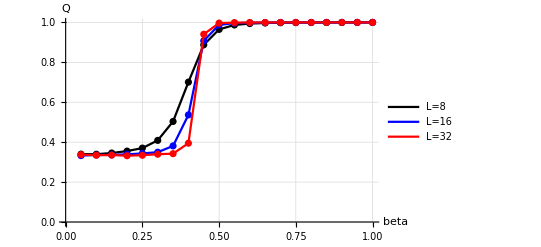

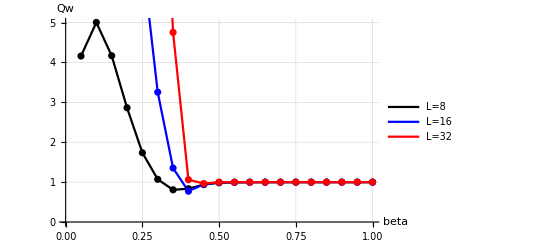

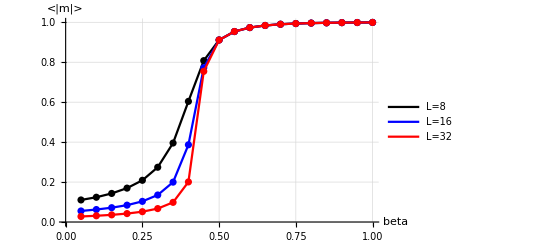

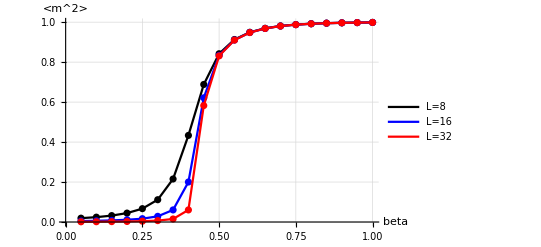

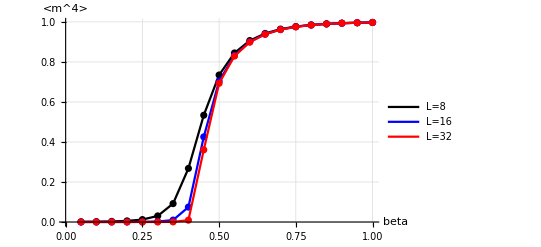

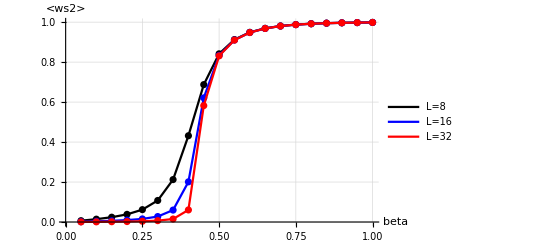

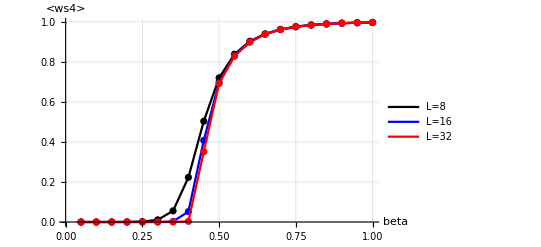

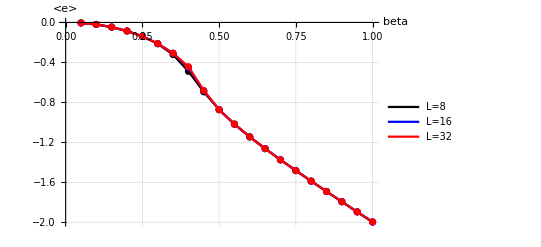

```mathematica
Show[ListLinePlot[Transpose[{beta,measure8[[11]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[11]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[11]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[11]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[11]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[11]]}],PlotStyle->Red],AxesLabel->{"beta","Q"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[12]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[12]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[12]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[12]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[12]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[12]]}],PlotStyle->Red],AxesLabel->{"beta","Qw"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[8]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[8]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[8]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[8]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[8]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[8]]}],PlotStyle->Red],AxesLabel->{"beta","<|m|>"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[1]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[1]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[1]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[1]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[1]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[1]]}],PlotStyle->Red],AxesLabel->{"beta","<m^2>"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[2]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[2]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[2]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[2]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[2]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[2]]}],PlotStyle->Red],AxesLabel->{"beta","<m^4>"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[3]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[3]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[3]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[3]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[3]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[3]]}],PlotStyle->Red],AxesLabel->{"beta","<ws2>"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[4]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[4]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[4]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[4]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[4]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[4]]}],PlotStyle->Red],AxesLabel->{"beta","<ws4>"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[5]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[5]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[5]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[5]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[5]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[5]]}],PlotStyle->Red],AxesLabel->{"beta","<e>"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[6]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[6]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[6]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[6]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[6]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[6]]}],PlotStyle->Red],AxesLabel->{"beta","<e2>"},LabelStyle->"Input",GridLines->Automatic]
Show[ListLinePlot[Transpose[{beta,measure8[[7]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,measure8[[7]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,measure16[[7]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,measure16[[7]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,measure32[[7]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,measure32[[7]]}],PlotStyle->Red],AxesLabel->{"beta","MaxCluster"},LabelStyle->"Input",GridLines->Automatic,PlotRange->All]
Show[ListLinePlot[Transpose[{beta,beta^2*measure8[[13]]}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,beta^2*measure8[[13]]}],PlotStyle->Black],ListLinePlot[Transpose[{beta,beta^2*measure16[[13]]}],PlotStyle->Blue,PlotLegends->{"L=16"}]~Show~ListPlot[Transpose[{beta,beta^2*measure16[[13]]}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,beta^2*measure32[[13]]}],PlotStyle->Red,PlotLegends->{"L=32"}]~Show~ListPlot[Transpose[{beta,beta^2*measure32[[13]]}],PlotStyle->Red],AxesLabel->{"beta","Cv"},LabelStyle->"Input",GridLines->Automatic,PlotRange->All]
Show[ListLinePlot[Transpose[{beta,beta*(measure8[[1]]-measure8[[8]]^2)}],PlotStyle->Black,PlotLegends->{"L=8"}]~Show~ListPlot[Transpose[{beta,beta*(measure8[[1]]-measure8[[8]]^2)}],PlotStyle->Black],ListLinePlot[Transpose[{beta,beta*(measure16[[1]]-measure16[[8]]^2)}],PlotStyle->Blue,PlotLegends->{"L=16"},PlotRange->All]~Show~ListPlot[Transpose[{beta,beta*(measure16[[1]]-measure16[[8]]^2)}],PlotStyle->Blue],ListLinePlot[Transpose[{beta,beta*(measure32[[1]]-measure32[[8]]^2)}],PlotStyle->Red,PlotLegends->{"L=32"},PlotRange->All]~Show~ListPlot[Transpose[{beta,beta*(measure32[[1]]-measure32[[8]]^2)}],PlotStyle->Red],AxesLabel->{"beta","χ"},LabelStyle->"Input",GridLines->Automatic,PlotRange->All]
```